# Motorbike net2 & net3

## Set Environment

```mathematica
home = "Y:/vault/pami/single_airplane_400/";workdir = "C:/users/lichao/git/geonb/";
SetDirectory[workdir];Needs["Posecpp`","posecpp_network.wl"];
```

```mathematica
prefix = "";suffix="_64";
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{76725,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.4];g2 = Graph[el2,VertexLabels->"Name"];(* for quad 64pix case*)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,0.9];g2 = Graph[el2,VertexLabels->"Name"];(* for quad 64pix car case*)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.7];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
(* for quad 64pix airplane case*)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.8];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
(* for quad 64pix face case*)
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

198

1261

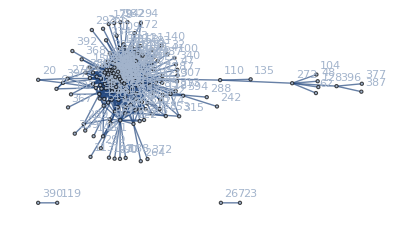

```mathematica
g2
```

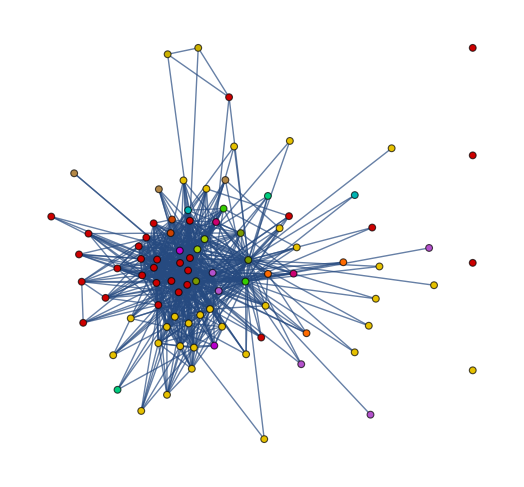

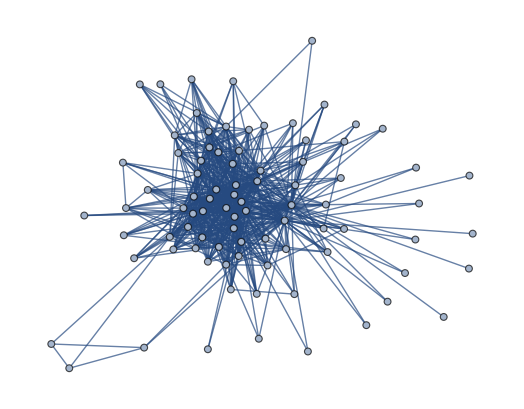

```mathematica
interGraph = Subgraph[g2,VertexList[g3]];
HighlightGraph[interGraph,comp3]
newg2= Subgraph[g2,ConnectedComponents[interGraph][[1]]]
```

```mathematica
VertexCount[newg2]
EdgeCount[newg2]
```

86

730

```mathematica
Export[home<>prefix<>"net2_plot"<>suffix<>".pdf",g2]
```

Export::noopen: Cannot open "Y:/vault/pami/single_car_400/net2_plot_64.pdf".

$Failed

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{592,608,623,744,240,446,312,735,564,691,85,90,768,558,715,797,772,536,347,742,94,132,565,251,201,701,631,527,404,250,295,791,383,109,71,133,72,279,157,612,286,268,759,426,148,416,369,47,567,514,478,303,55,252,569,82,40,475,516,402,158,393,189,63,37,92,282,621,67,466,297,333,579,367,229,410,719,76,774,594,490,315,262,644,535,206,136,89,389,9,541,790,603,171,664,16,507,321,294,628,156,755,651,414,233,14,457,264,241,36,2,705,613,771,582,625,220,578,17,690,679,515,745,451,423,276,729,551,198,197,153,635,118,105,20,682,661,575,746,555,552,543,642,439,406,365,336,357,655,632,191,353,152,145,140,112,311,761,35,756,680,600,780,724,670,611,591,559,713,432,430,549,352,337,317,289,273,248,654,318,210,202,188,186,185,182,177,159,126,123,640,86,66,58,57,53,44,39,22}

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[newg2]]
```

Y:/vault/pami/single_airplane_400/net2_el_64.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_03_02"<>suffix<>".txt"]
```

{4<->66,4<->207,4<->255,4<->298,28<->194,28<->256,28<->356,28<->364,28<->382,31<->332,45<->56,45<->248,45<->321,45<->361,49<->184,49<->251,49<->292,54<->136,54<->195,54<->248,54<->357,56<->248,56<->321,56<->330,56<->361,65<->73,65<->177,65<->241,65<->284,65<->364,65<->365,66<->207,66<->255,68<->195,68<->199,68<->210,68<->251,68<->259,68<->280,68<->292,73<->252,74<->163,74<->221,75<->256,76<->177,76<->354,83<->175,84<->149,99<->290,99<->292,99<->321,99<->330,99<->357,101<->251,117<->244,123<->149,130<->215,131<->137,136<->195,137<->198,139<->250,149<->199,152<->336,154<->321,158<->175,163<->194,163<->221,163<->284,174<->194,174<->356,174<->364,174<->365,174<->382,175<->177,177<->234,178<->330,181<->194,181<->261,181<->341,184<->210,184<->251,184<->290,184<->292,184<->357,194<->256,194<->284,194<->364,194<->365,194<->382,195<->259,195<->357,199<->259,210<->251,210<->292,219<->251,219<->292,221<->241,222<->225,222<->309,223<->386,248<->321,248<->357,248<->361,251<->280,251<->292,251<->338,251<->363,256<->287,256<->382,260<->380,261<->341,261<->382,276<->397,280<->363,281<->365,284<->301,284<->364,284<->365,290<->292,290<->330,290<->357,292<->338,292<->357,292<->363,300<->332,321<->330,321<->361,322<->359,330<->357,330<->361,356<->382,364<->365}

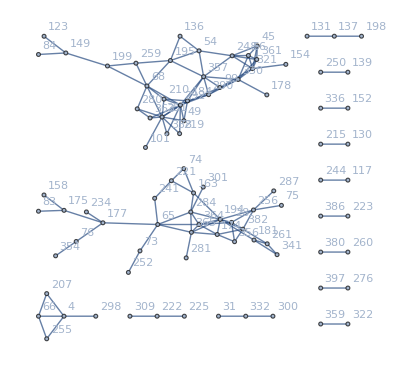

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
```

189

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{290,99,184,292,330,357,321,49,210,251,68,219,338,363,56,178,361,54,195,248,45,154,101,280,199,259,136,149,84,123},{354,76,177,65,175,234,73,241,284,364,365,83,158,252,221,163,194,301,28,174,281,74,181,256,382,356,261,341,75,287},{298,4,66,207,255},{131,137,198},{31,332,300},{309,222,225},{336,152},{117,244},{223,386},{130,215},{322,359},{260,380},{250,139},{276,397}}

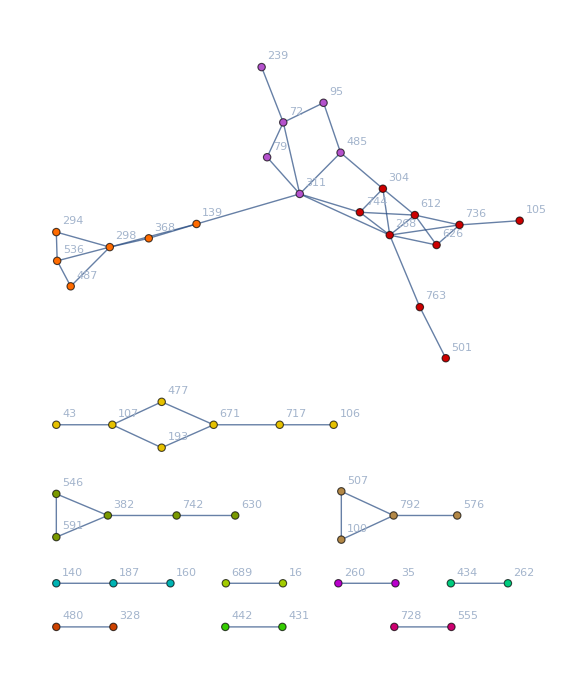

```mathematica
HighlightGraph[g3,comp3,ImageSize->Large]
```

```mathematica
Export[home<>prefix<>"net3_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/net3_plot_64.pdf

```mathematica
comp3=FindGraphCommunities[Graph[el3]]
```

{{247,7,9,59,64,135,290,443,796,116,166,274,354,683,18,731,21,25,37,134,171,195,293,310,311,331,333,485,568,570,729,30,316,392,153,188,328,352,608,708,33,67,678,415,55,264,279,540,606,785,571,233,306,414,566,726,261,88,489,106,110,297,130,266,431,439,490,145,296,495,252,691,154,157,738,200,730,703,590,762,258,599,474,629,778,376,744,391,401,533},{191,49,287,756,601,68,92,209,372,404,484,712,175,349,422,579,102,309,694,104,387,465,680,716,109,713,167,234,432,692,177,632,423,779,238,786,276,285,478,526,573,797,302,342,389,745,394,360,798,368,584,408,641,508,457,567,701,676},{16,32,122,222,256,292,402,767,510,655,718,26,40,70,98,173,189,220,291,305,361,403,406,501,31,61,156,253,447,728,81,149,374,452,530,547,36,343,464,638,503,85,380,385,519,87,93,246,185,517,609,597,659},{3,363,491,43,725,307,89,94,127,165,221,357,164,362,399,643,180,183,607,639,782,317,324,545,449,497,635,618},{1,113,481,535,22,418,532,563,628,689,774,184,334,358,69,522,675,91,520,142,179,259,241,687,326,611,440},{28,72,29,136,476,44,359,732,107,128,303,323,416,614,753,429,577,653},{112,181,260,219,304,318,705,211,466,529,582},{6,215,420},{83,379,272},{345,398,543},{42,759},{229,685},{330,720},{467,513},{263,521},{453,511},{654,772},{707,757}}

```mathematica
comp3//Length
```

18

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x"<>suffix<>".txt",home<>prefix<>"converge_y"<>suffix<>".txt",home<>prefix<>"converge_s"<>suffix<>".txt",home<>prefix<>"converge_n"<>suffix<>".txt"];
```

```mathematica
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,{Keys[gx],VertexList[g3]},{2}],PlotStyle->{Blue,Red}]
```

```mathematica
Export[home<>prefix<>"global_summary"<>suffix<>".txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

Y:/vault/pami/single_car_400/global_summary_64.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{31,58,59,245,292,559,638},{15,55,180,206,430,695},{7,43,120,374,722},{89,395,652},{33,62},{133,482},{136,333},{456,745},{641,733}}

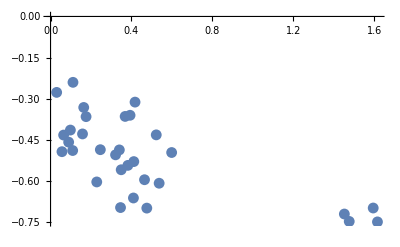

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,VertexList[g3]],PlotRange->All]
```

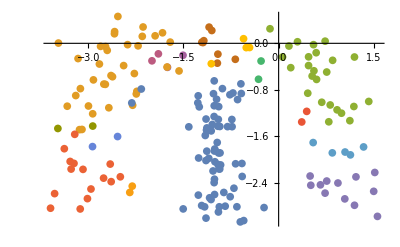

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}],PlotRange->All]
```

```mathematica
Export[home<>prefix<>"gps_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/gps_plot_64.pdf

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

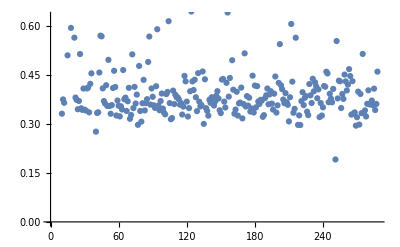

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

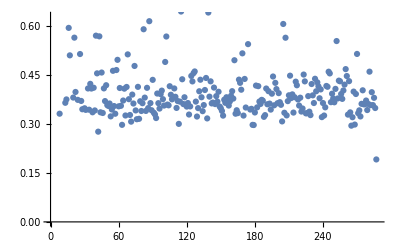

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

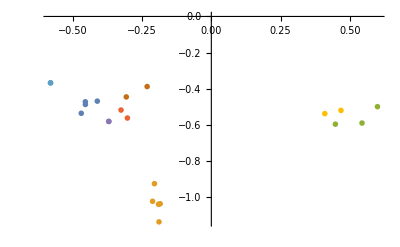

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>1&]
```

{{1,2,4,8,11,24,26,30,35,39,42,69,70,73,76,77,78,92,106,110,111,124,131,132,137,142,149,153,157,162,165,174,177,182,183,184,188,193,203,205,216,223,228,229,231,243,264,269,271,273,288,291,303,312,313,314,316,318,321,325,327,359,361,367,370,386,387,397},{5,21,47,55,63,72,94,97,141,187,208,220,230,249,250,261,267,274,280,283,292,294,307,309,315,323,329,333,339,344,360,366,382,389},{7,15,29,38,43,58,74,83,104,105,164,169,192,224,241,242,251,287,332,358,362,374,383,394,396},{27,31,44,46,56,103,125,139,156,211,256,276,286,311,328},{28,85,112,145,172,186,232,248,346,356,375,399},{10,13,40,127,152,221,297,331},{33,68,150,158,388},{114,161,239,265},{151,171},{170,277},{190,353},{36,302},{87,364},{198,212},{268,322},{71,215},{18,130}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],Log[gs[#]]}&,voroComms,{2}]
```

{{-1.55657,1.26192,0.171183},{-3.26302,-0.182251,0.225913},{0.0377788,-0.0566599,0.193706},{-3.67811,1.69225,0.167772},{0.444264,1.93442,0.120528},{-1.62523,-0.554699,0.150122},{0.376783,1.22702,0.184625},{-1.42449,-0.674062,0.430874},{-2.44784,-0.508976,0.492225},{-3.75071,0.898317,0.0863309},{-0.413241,0.444352,0.489351},{-3.66393,0.762204,0.614307},{-2.9428,1.89455,0.207147},{-2.51567,-0.328446,0.129943},{-1.18562,-0.427581,0.568271},{-2.93097,0.214246,0.318026},{-2.46376,-0.358043,0.468305}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

17

```mathematica
Export[home<>prefix<>"voro_centers"<>suffix<>".txt",centers]
```

Y:/vault/pami/single_car_400/voro_centers_64.txt